```mathematica
SetDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]];
```

## Import Data

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Vdata=SplitBy[Import["latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ReVdataT[n_]:=Table[Vdata[[n,x,2;;3]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTe[n_]:=Table[Vdata[[n,x,2;;4]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTn[n_]:=ReVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ReVdataTne[n_]:=ReVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};

T0data=Join[{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT41.05.dat","Table"][[All,1;;3]]},{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT71.54.dat","Table"][[All,1;;3]]}];
T0data=T0data/.{a_,b_,c_}:>{a/0.197327,b,c};
```

## Define functions for real part

```mathematica
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r+(2 σ)/m-(ⅇ^(-m r) (2+m r) σ)/m+c;
```

```mathematica
Limit[ReV[r,m,α,σ,c],m->0]
```

c-α/r+r σ

```mathematica
ReVm0[r_,α_,σ_,c_]:=c-α/r+σ r;
```

## Low T Cornell Fitting & Interpolation

```mathematica
T0datarand[n_]:=Table[{T0data[[n]][[i,1]],RandomVariate[NormalDistribution[T0data[[n]][[i,2]],T0data[[n]][[i,3]]]]},{i,Length[T0data[[n]]]}]
```

### beta = 6.9 Fitting

```mathematica
VaryFitLow=Range[2,4];
VaryFitHigh=Range[20,28];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];

VaryFitLowAR={2,2,2,2,2,1,3,1,3}+1;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}-2;
```

#### Varied Weights (not in use)

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

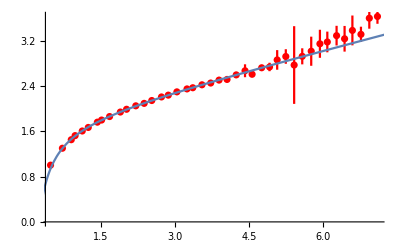

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

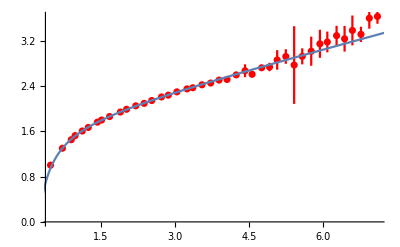

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

-Graphics-

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

-Graphics-

#### Use this one!

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
res=Reap[Parallelize[Do[Block[{fit0,fit,al0,sig0,const0,al,sig,const},fit0=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{{al,al0},{sig,sig0},{const,const0}},r];
ParallelSow[al/.fit["BestFitParameters"],a];
ParallelSow[sig/.fit["BestFitParameters"],s];
ParallelSow[const/.fit["BestFitParameters"],c];],{ii,1,100},{i,1,Length[VaryFit]}]],{a,s,c}];//AbsoluteTiming
αfinal69r={Mean[res[[2,1,1]]],StandardDeviation[res[[2,1,1]]]}
σfinal69r={Mean[res[[2,2,1]]],StandardDeviation[res[[2,2,1]]]}
cfinal69r={Mean[res[[2,3,1]]],StandardDeviation[res[[2,3,1]]]}
Clear[res];
```

{23.8309,Null}

{0.444182,0.0468765}

{0.224342,0.0165353}

{1.7499,0.0605475}

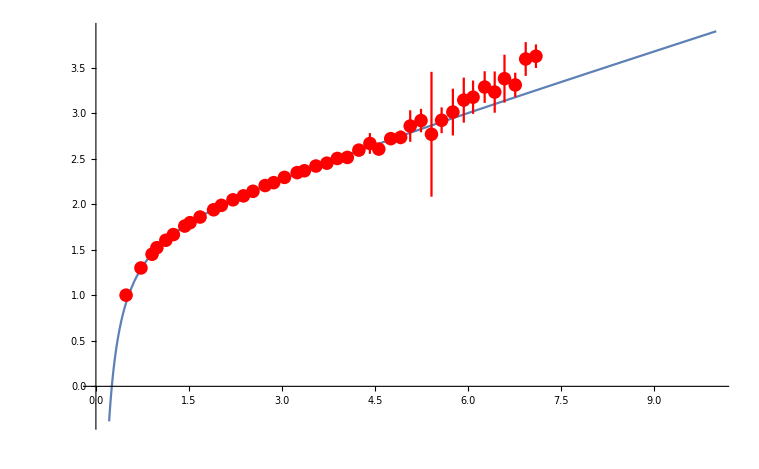

```mathematica
Show[{Plot[ReVm0[r,αfinal69r[[1]],σfinal69r[[1]],cfinal69r[[1]]],{r,0,10}],ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All]}]
```

### beta = 7.4 Fitting

```mathematica
VaryFitLow=Range[5,7];
VaryFitHigh=Range[26,34];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
```

```mathematica
VaryFitLowAR={2,2,2,2,2,1,3,1,3}+4;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}+4;
```

#### Varied Weights (not in use)

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

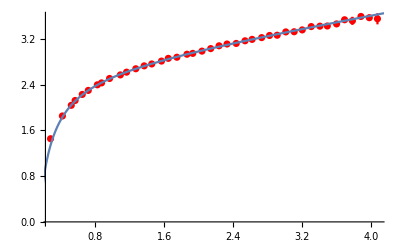

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

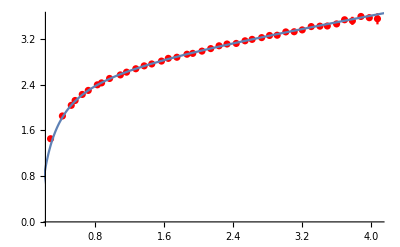

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

-Graphics-

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

-Graphics-

#### Use this one!

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
res=Reap[Parallelize[Do[Block[{fit0,fit,al0,sig0,const0,al,sig,const},fit0=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{{al,al0},{sig,sig0},{const,const0}},r];
ParallelSow[al/.fit["BestFitParameters"],a];
ParallelSow[sig/.fit["BestFitParameters"],s];
ParallelSow[const/.fit["BestFitParameters"],c];],{ii,1,100},{i,1,Length[VaryFit]}]],{a,s,c}];//AbsoluteTiming
αfinal748r={Mean[res[[2,1,1]]],StandardDeviation[res[[2,1,1]]]}
σfinal748r={Mean[res[[2,2,1]]],StandardDeviation[res[[2,2,1]]]}
cfinal748r={Mean[res[[2,3,1]]],StandardDeviation[res[[2,3,1]]]}
Clear[res];
```

{16.2346,Null}

{0.384617,0.0270857}

{0.264714,0.0143831}

{2.64761,0.04217}

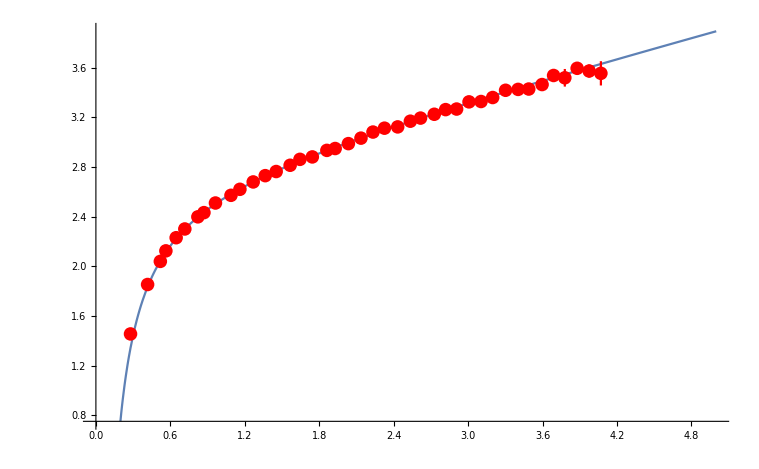

```mathematica
Show[{Plot[ReVm0[r,αfinal748r[[1]],σfinal748r[[1]],cfinal748r[[1]]],{r,0,5}],ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All]}]
```

### Linear Interpolation

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
```

```mathematica
btinter=Interpolation[Transpose[{T,β}]];
btinter1=Interpolation[Transpose[{T,β}],InterpolationOrder->1];
```

```mathematica
beta2T0res={αfinal69r,σfinal69r,cfinal69r};
beta7T0res={αfinal748r,σfinal748r,cfinal748r};
```

```mathematica
T0constfit={LinearModelFit[{{β[[2]],beta2T0res[[1,1]]},{β[[7]],beta7T0res[[1,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,1]]},{β[[7]],beta7T0res[[2,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,1]]},{β[[7]],beta7T0res[[3,1]]}},x,x]};
T0errfit={LinearModelFit[{{β[[2]],beta2T0res[[1,2]]},{β[[7]],beta7T0res[[1,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,2]]},{β[[7]],beta7T0res[[2,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,2]]},{β[[7]],beta7T0res[[3,2]]}},x,x]};
```

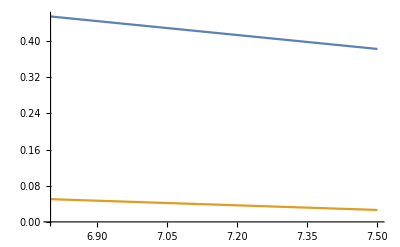

```mathematica
Plot[{T0constfit[[1]][x],T0errfit[[1]][x]},{x,6.8,7.5}]
```

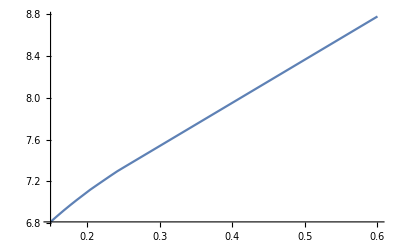

```mathematica
Plot[btinter1[x],{x,0.15,0.6}]
```

```mathematica
Table[T0constfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.217381,0.224342,0.231303,0.240004,0.248704,0.252185,0.264714}

```mathematica
Table[T0errfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.0169063,0.0165353,0.0161642,0.0157004,0.0152365,0.015051,0.0143831}

```mathematica
Tscanc=Table[i,{i,0.15,0.25,0.003}]
```

{0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249}

```mathematica
Tscanb=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
βTscanc=Table[btinter[i],{i,0.15,0.25,0.003}]
```

{6.81385,6.8325,6.85091,6.86907,6.887,6.9047,6.92218,6.93945,6.95652,6.97339,6.99007,7.00662,7.02305,7.03931,7.05539,7.0713,7.08702,7.10256,7.1179,7.13291,7.1476,7.16212,7.17648,7.19072,7.20484,7.21888,7.23284,7.24676,7.26075,7.2747,7.28855,7.30228,7.31589,7.32936}

```mathematica
βTscanc1=Table[btinter1[i],{i,0.15,0.25,0.003}]
```

{6.81341,6.83171,6.85,6.86829,6.88659,6.90455,6.92159,6.93864,6.95568,6.97273,6.98977,7.00636,7.02225,7.03814,7.05403,7.06992,7.08581,7.10169,7.11758,7.1326,7.14686,7.16112,7.17538,7.18964,7.2039,7.21816,7.23241,7.24667,7.26065,7.27454,7.28843,7.30206,7.31445,7.32683}

```mathematica
βTscanb=Join[Table[btinter[i],{i,0.15,0.285,0.005}],Table[btinter1[i],{i,0.29,0.6,0.005}]]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81385,6.8448,6.87507,6.9047,6.93372,6.96216,6.99007,7.01759,7.04469,7.0713,7.0974,7.12298,7.1476,7.17171,7.19544,7.21888,7.24212,7.26541,7.28855,7.31137,7.33382,7.35585,7.3774,7.39842,7.41885,7.43864,7.45773,7.47607,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
βTscanb1=Table[btinter1[i],{i,0.15,0.6,0.005}]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81341,6.8439,6.87439,6.90455,6.93295,6.96136,6.98977,7.01695,7.04343,7.06992,7.0964,7.12288,7.14686,7.17063,7.19439,7.21816,7.24192,7.26528,7.28843,7.31032,7.33096,7.35161,7.37225,7.39289,7.41353,7.43417,7.45482,7.47546,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
Table[T0constfit[[2]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.218345,0.219644,0.220925,0.222189,0.223437,0.224669,0.225886,0.227088,0.228276,0.22945,0.230612,0.231763,0.232907,0.234039,0.235158,0.236265,0.23736,0.238441,0.23951,0.240554,0.241577,0.242587,0.243587,0.244578,0.245561,0.246538,0.24751,0.248479,0.249453,0.250424,0.251388,0.252344,0.253291,0.254229}

```mathematica
Table[T0constfit[[1]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.453029,0.451113,0.449223,0.447358,0.445517,0.443699,0.441904,0.44013,0.438378,0.436645,0.434931,0.433232,0.431545,0.429875,0.428224,0.42659,0.424975,0.42338,0.421804,0.420262,0.418754,0.417263,0.415788,0.414326,0.412875,0.411434,0.41,0.408571,0.407133,0.405701,0.404279,0.402869,0.401471,0.400088}

```mathematica
Table[T0constfit[[3]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{1.61656,1.64543,1.67392,1.70203,1.72978,1.75718,1.78423,1.81096,1.83738,1.86349,1.88932,1.91493,1.94035,1.96552,1.99041,2.01503,2.03937,2.06342,2.08717,2.1104,2.13313,2.1556,2.17784,2.19987,2.22173,2.24346,2.26507,2.28661,2.30827,2.32986,2.35129,2.37254,2.39361,2.41446}

```mathematica
Table[T0constfit[[2]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.218345,0.2205,0.222607,0.224669,0.226689,0.228669,0.230612,0.232527,0.234413,0.236265,0.238082,0.239863,0.241577,0.243255,0.244907,0.246538,0.248156,0.249777,0.251388,0.252976,0.254539,0.256072,0.257572,0.259035,0.260458,0.261835,0.263164,0.264441,0.265835,0.267272,0.268709,0.270145,0.271582,0.273019,0.274456,0.275893,0.27733,0.278766,0.280203,0.28164,0.283077,0.284514,0.285951,0.287387,0.288824,0.290261,0.291698,0.293135,0.294572,0.296009,0.297445,0.298882,0.300319,0.301756,0.303193,0.30463,0.306066,0.307503,0.30894,0.310377,0.311814,0.313251,0.314688,0.316124,0.317561,0.318998,0.320435,0.321872,0.323309,0.324745,0.326182,0.327619,0.329056,0.330493,0.33193,0.333366,0.334803,0.33624,0.337677,0.339114,0.340551,0.341988,0.343424,0.344861,0.346298,0.347735,0.349172,0.350609,0.352045,0.353482,0.354919}

```mathematica
Table[T0constfit[[1]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.453029,0.44985,0.446742,0.443699,0.440719,0.437798,0.434931,0.432105,0.429323,0.42659,0.423909,0.421283,0.418754,0.416278,0.413841,0.411434,0.409047,0.406655,0.404279,0.401935,0.39963,0.397367,0.395154,0.392996,0.390897,0.388865,0.386904,0.385021,0.382964,0.380844,0.378724,0.376604,0.374484,0.372365,0.370245,0.368125,0.366005,0.363885,0.361765,0.359645,0.357525,0.355405,0.353286,0.351166,0.349046,0.346926,0.344806,0.342686,0.340566,0.338446,0.336326,0.334207,0.332087,0.329967,0.327847,0.325727,0.323607,0.321487,0.319367,0.317247,0.315128,0.313008,0.310888,0.308768,0.306648,0.304528,0.302408,0.300288,0.298168,0.296049,0.293929,0.291809,0.289689,0.287569,0.285449,0.283329,0.281209,0.279089,0.27697,0.27485,0.27273,0.27061,0.26849,0.26637,0.26425,0.26213,0.260011,0.257891,0.255771,0.253651,0.251531}

```mathematica
Table[T0constfit[[3]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{1.61656,1.66447,1.71132,1.75718,1.80209,1.84612,1.88932,1.93191,1.97385,2.01503,2.05543,2.09502,2.13313,2.17045,2.20718,2.24346,2.27944,2.31548,2.35129,2.38661,2.42136,2.45545,2.48881,2.52134,2.55297,2.5836,2.61315,2.64153,2.67253,2.70448,2.73643,2.76838,2.80033,2.83228,2.86423,2.89618,2.92813,2.96008,2.99203,3.02398,3.05593,3.08788,3.11983,3.15178,3.18373,3.21568,3.24763,3.27958,3.31152,3.34347,3.37542,3.40737,3.43932,3.47127,3.50322,3.53517,3.56712,3.59907,3.63102,3.66297,3.69492,3.72687,3.75882,3.79077,3.82272,3.85467,3.88662,3.91857,3.95051,3.98246,4.01441,4.04636,4.07831,4.11026,4.14221,4.17416,4.20611,4.23806,4.27001,4.30196,4.33391,4.36586,4.39781,4.42976,4.46171,4.49366,4.52561,4.55756,4.5895,4.62145,4.6534}

## Debye Fitting

```mathematica
ReVdataTnrand[n_]:=Table[{ReVdataTne[n][[i,1]],RandomVariate[NormalDistribution[ReVdataTne[n][[i,2]],ReVdataTne[n][[i,3]]]]},{i,Length[ReVdataTne[n]]}]
```

```mathematica
T0constrand[n_]:={RandomVariate[NormalDistribution[T0constfit[[1]][β[[n]]],T0errfit[[1]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[2]][β[[n]]],T0errfit[[2]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[3]][β[[n]]],T0errfit[[3]][β[[n]]]]]}
```

```mathematica
VaryFitLow=Range[1,3];
VaryFitHigh=Range[18,30];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
mdfitrand[n_,runs_]:=Block[{res},res=Reap[ParallelDo[ParallelSow[Quiet[m/.NonlinearModelFit[ReVdataTnrand[n][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReV[r,m,T0constrand[n][[1]],T0constrand[n][[2]],T0constrand[n][[3]]],{{m,0.1}},r]["BestFitParameters"]],m],{ii,1,runs},{i,1,Length[VaryFit]}],m];
Return[{Mean[res[[2,1]]],StandardDeviation[res[[2,1]]]}]]
```

```mathematica
mdfitrandfinal=ConstantArray[0,Length[Vdata]];
```

```mathematica
mdfitrandfinal[[1]]=mdfitrand[1,1000]
```

{0.0751197,0.107025}

```mathematica
mdfitrandfinal[[2]]=mdfitrand[2,1000]
```

{0.190375,0.142619}

```mathematica
mdfitrandfinal[[3]]=mdfitrand[3,1000]
```

{0.255831,0.152087}

```mathematica
mdfitrandfinal[[4]]=mdfitrand[4,1000]
```

{0.376999,0.184038}

```mathematica
mdfitrandfinal[[5]]=mdfitrand[5,1000]
```

{0.530692,0.15114}

```mathematica
mdfitrandfinal[[6]]=mdfitrand[6,1000]
```

{0.542501,0.17123}

```mathematica
mdfitrandfinal[[7]]=mdfitrand[7,1000]
```

{0.667435,0.176338}

```mathematica
mdfitrandfinal={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}}(*10k run*)
```

{{0.0389196,0.0674368},{0.125821,0.109232},{0.189258,0.128528},{0.30988,0.183581},{0.48026,0.14797},{0.496572,0.179178},{0.646507,0.179859}}

```mathematica
(*Plot[{ReV[r,mdfitrandfinal[[2,1]],T0constfit[[1]][β[[2]]],T0constfit[[2]][β[[2]]],T0constfit[[3]][β[[2]]]],ReV[r,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],T0constfit[[3]][β[[3]]]],ReV[r,mdfitrandfinal[[4,1]],T0constfit[[1]][β[[4]]],T0constfit[[2]][β[[4]]],T0constfit[[3]][β[[4]]]],ReV[r,mdfitrandfinal[[5,1]],T0constfit[[1]][β[[5]]],T0constfit[[2]][β[[5]]],T0constfit[[3]][β[[5]]]],,ReV[r,mdfitrandfinal[[6,1]],T0constfit[[1]][β[[6]]],T0constfit[[2]][β[[6]]],T0constfit[[3]][β[[6]]]],ReV[r,mdfitrandfinal[[7,1]],T0constfit[[1]][β[[7]]],T0constfit[[2]][β[[7]]],T0constfit[[3]][β[[7]]]]},{r,0,10}]*)
```

```mathematica
mdfitAR={0.006612808256711139,0.11838248788551524,0.1870803288935863,0.26288830333533697,0.4797079970797252,0.4971567199527494,0.6554067022426473};
```

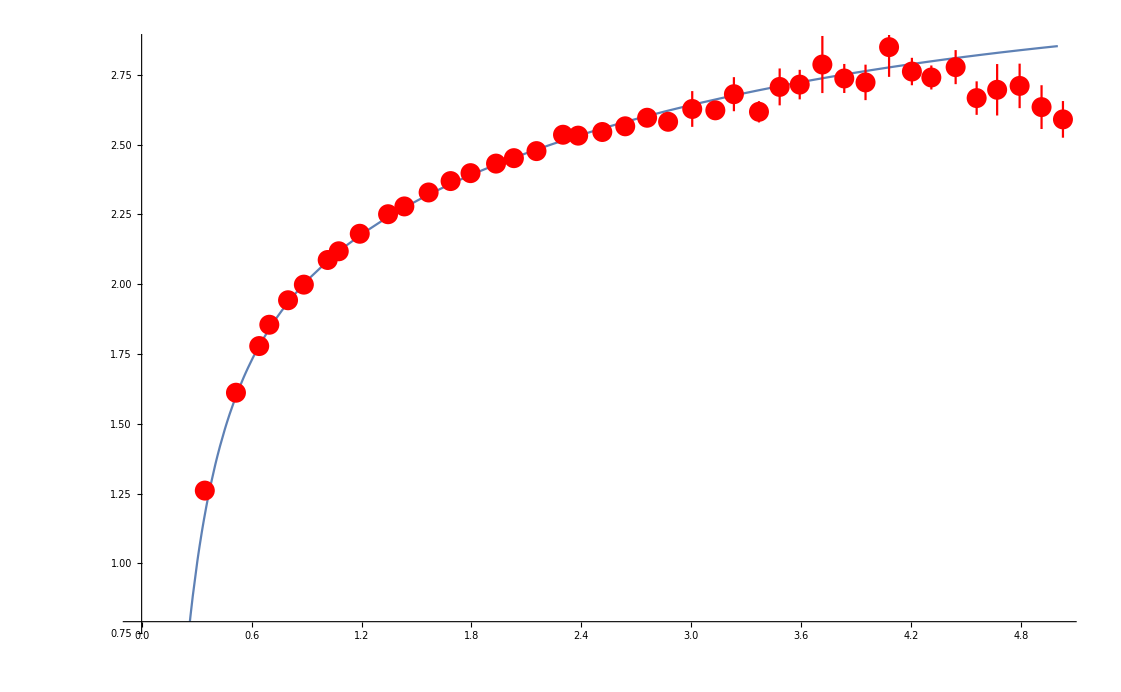

```mathematica
Block[{n=5},Show[Plot[ReV[r,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]],{r,0,5}],ErrorListPlot[ReVdataTne[n],PlotStyle->{Red},PlotRange->All]]]
```

## Plotting of imaginary part

```mathematica
ImVc[r_,mD_,α_,T_]:=T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞},MaxRecursion->20];
```

```mathematica
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImV[r_,mD_,α_,σ_,T_]:=T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞},MaxRecursion->20]+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
g[s_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p s],{p,0,∞}]];
```

```mathematica
ImVold[r_,mD_,α_,σ_,T_]:=T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞},MaxRecursion->20]-α T (ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,(mD^2 σ/α)^(1/4)r},MaxRecursion->20,WorkingPrecision->10]]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,(mD^2 σ/α)^(1/4)r,∞},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,√2 0]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,∞},MaxRecursion->20,WorkingPrecision->10]]);
```

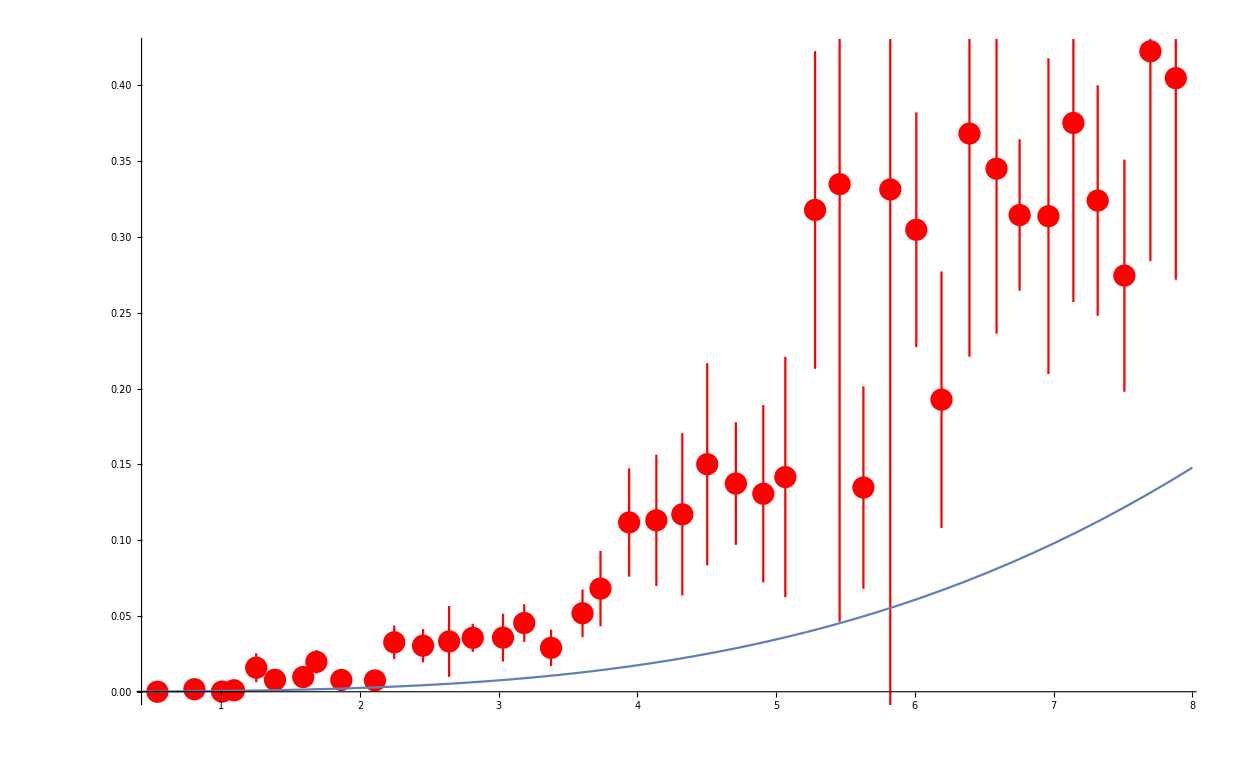

```mathematica
Block[{n=1},Show[ErrorListPlot[ImVdataTne[n],PlotStyle->{Red},PlotRange->All],Plot[ImV[r,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T[[n]]],{r,0,8}]]]
```

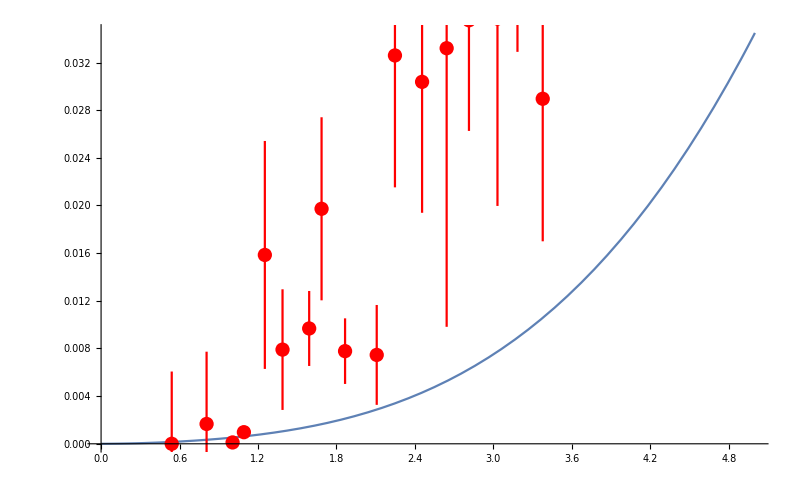

```mathematica
Block[{n=1},Show[Plot[ImV[r,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T[[n]]],{r,0,5}],ErrorListPlot[ImVdataTne[n],PlotStyle->{Red},PlotRange->All]]]
```

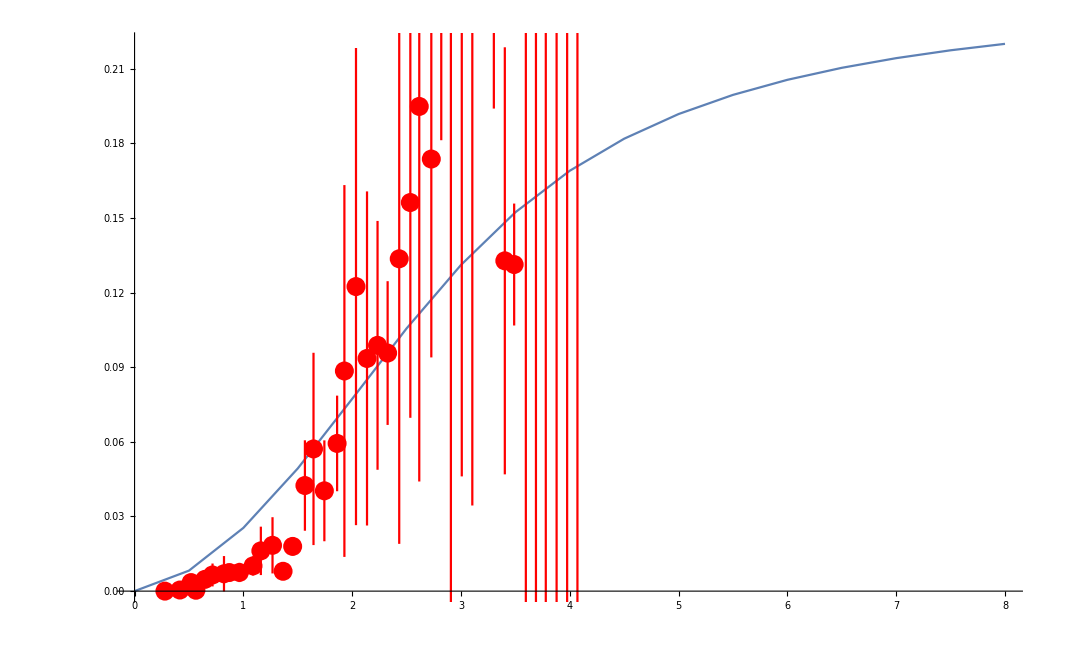

```mathematica
Block[{n=7},Show[DiscretePlot[ImVold[r,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T[[n]]],{r,0,8,1/2},Joined->True,Filling->None],ErrorListPlot[ImVdataTne[n],PlotStyle->{Red},PlotRange->All]]]
```